## init

```mathematica
SetDirectory["C:\\Users\\brenton\\DeadlockWorkspace\\transcripts\\"]
```

C:\Users\brenton\DeadlockWorkspace\transcripts

```mathematica
names=FileNames["transcript-*.txt",""];
```

```mathematica
counts={#,Flatten[StringCases[ReadList[#,String],"hardest is "~~Shortest[a__]~~" moves":>ToExpression[a]]]}&/@names;
```

```mathematica
firstBoardChar[s_String]:=StringMatchQ[StringTake[s,1],"/"|"|"|"\\"|"Y"|"J"|"K"]
```

```mathematica
readBoardsFromTranscript[f_]:=(
Reap[
id=StringDrop[StringDrop[f,11],-4];
Pint[id];
Catch[
While[True,
r=Read[f,String];
Which[
r===EndOfFile,Break[],
StringMatchQ[r,"generating partition #"~~__],(
p=StringCases[r,"generating partition #"~~p__:>p][[1]];
Pint["partition "<>p];
r=Read[f,String];
Which[
StringMatchQ[r,"idhash "~~__~~"hardest is "~~(NumberString)~~__],(
moves=StringCases[r,"idhash "~~__~~"hardest is "~~m:NumberString~~__:>m][[1]];
board=Read[f,{String,String,String,String,String,String,String,String}];
If[And@@(firstBoardChar/@board),Sow[{{"id"->id,"partition"->p,"moves"->moves},board}],Throw[{"not a board",board},1]]
),
StringMatchQ[r,"idhash "~~__~~"hardest is null"~~__],Null,
True,Throw[{"1",r},1]
]
)
]
]
,
1
,
Print["bad",#]&
];
Close[f];
Null
][[2,1]]
)
```

## data

```mathematica
Sort[Flatten[counts[[All,2]]]]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,«50998»,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,65,65,65,65,65,65,65,65,65,65,65,65,66,66,66,66,66,66,66,66,66,66,66,67,67,67,67,67,67,67,67,67,67,68,68,68,68,68,69,69,69,70,70,70,71,71,71,71,71,71,71,71,71,71,72,72,73,73,74,74,74,74,74,74,74,74,75,75,76,76,76,76,76,76,76,77,77,77,77,78,78,78,78,81,81,82,82,82,84,85,85,87,87,88,89,89,90,99}

```mathematica
Total[Length[#[[2]]]&/@counts]
```

51234

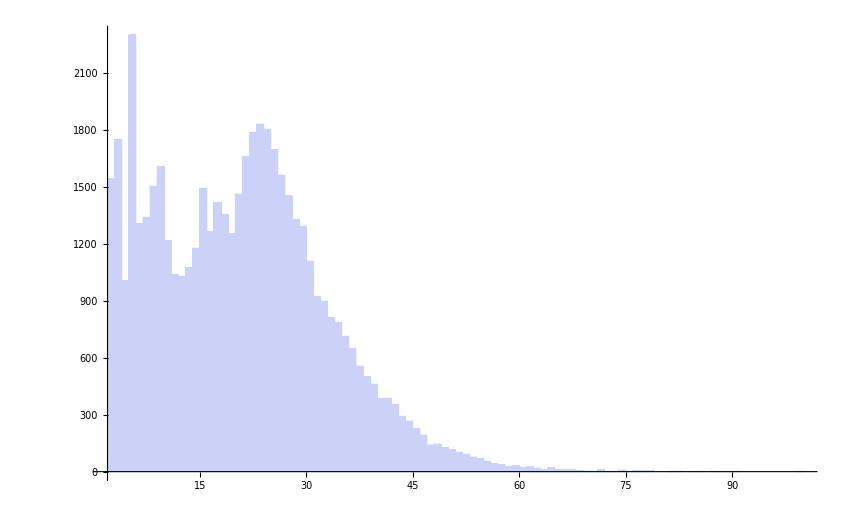

```mathematica
Histogram[Flatten[counts[[All,2]]]]
```

## generate .dat file name and contents

```mathematica
generateDatFileNamesAndContents[transcript_]:=
(
boards=readBoardsFromTranscript[transcript];
(
rules=#[[1]];
data=#[[2]];
file="gen-"<>("id"/.rules)<>"-"<>("partition"/.rules)<>".dat";
{file,"moves: "<>("moves"/.rules)<>"\n"<>StringJoin[((ToString[#]<>"\n")&/@data)]}
)&/@boards
)
```

## generate zip file

```mathematica
a=generateDatFileNamesAndContents[#]&/@names;
```

```mathematica
b=Flatten[a,1];
```

```mathematica
Length[b]
```

51234

```mathematica
StringReplace[b[[1,2]],"moves: "~~m:NumberString~~__:>m]
```

21

```mathematica
c=Select[b,ToExpression[StringReplace[#[[2]],"moves: "~~m:NumberString~~__:>m]]≥30&];
```

```mathematica
Length[c]
```

10743

```mathematica
d=c[[1;;100]];
```

```mathematica
AbsoluteTiming[Export["C:\\Users\\brenton\\DeadlockWorkspace\\DeadlockResources\\gen\\bin\\levels\\levels.zip",d[[All,2]],{"ZIP",{#,"Text"}&/@d[[All,1]]}]]
```

{1.977113,C:\Users\brenton\DeadlockWorkspace\DeadlockResources\gen\bin\levels\levels.zip}

## generate BoardsIndex.java

```mathematica
file="C:\\Users\\brenton\\DeadlockWorkspace\\DeadlockResources\\gen\\src\\com\\gutabi\\deadlock\\gen\\BoardsIndex.java";
WriteString[file,"package com.gutabi.deadlock.gen;

public class BoardsIndex {
\t
\tpublic static final String[] table = "<>ToString[StringTake[#,{5,-5}]&/@d[[All,1]],InputForm]<>";
\t
}
"];
Close[file]
```

C:\Users\brenton\DeadlockWorkspace\DeadlockResources\gen\src\com\gutabi\deadlock\gen\BoardsIndex.java

```mathematica
Streams[]
```

{OutputStream[stdout,1],OutputStream[stderr,2]}